```mathematica
DumpSave[NotebookDirectory[]<>"SE.mx","Global`"]
```

{Global`}

```mathematica
Get[NotebookDirectory[]<>"SE.mx"]
```

### API:

#### SVD

```mathematica
Hse[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,γ0_?NumberQ,ω0_,dim_?IntegerQ]:=Block[{t=25/a^2,μ=μ0,α=α0/(2a),Vz=V0,Δ=Δ0,γ=γ0,ω=ω0},KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]-γ(ω/(√(Δ^2-ω^2+1*^-9I))IdentityMatrix[4dim,SparseArray]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ/(√(Δ^2-ω^2+1*^-9I))IdentityMatrix[dim,SparseArray]]])-ω IdentityMatrix[4*dim,SparseArray]]
```

```mathematica
Hc[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,dim_?IntegerQ]:=Block[{t=25/a^2,μ=μ0,α=α0/(2a),Vz=V0,Δ=Δ0},KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ*IdentityMatrix[dim,SparseArray]]]]
```

```mathematica
singm[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,γ0_?NumberQ,ω0_?NumberQ,dim_?IntegerQ]:=singm[a,μ0,Δ0,V0,α0,γ0,ω0,dim]=SingularValueDecomposition[Hse[a,μ0,Δ0,V0,α0,γ0,ω0,dim],-1,Method->{"Arnoldi",MaxIterations->∞}][[2,1,1]]
```

```mathematica
froot[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,γ0_?NumberQ,dim_?IntegerQ]:=Block[{μ=μ0,α=α0,Vz=V0,Δ=Δ0,γ=γ0,list,pk,elist,roots,root},elist=Range[0,0.2,.005];list=ParallelTable[singm[a,μ,Δ,Vz,α,γ,i,dim],{i,elist}];pk=FindPeaks[-list];roots=elist[[pk[[All,1]]]];root=FindRoot[singm[a,μ,Δ,Vz,α,γ,i,dim],{i,#}]&/@roots;Union@root[[All,1,2]]]
```

```mathematica
frootz[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,γ0_?NumberQ,dim_?IntegerQ]:=Block[{μ=μ0,α=α0,Vz=V0,Δ=Δ0,γ=γ0},FindRoot[singm[a,μ,Δ,Vz,α,γ,i,dim],{i,0}][[1,2]]]
```

#### Iteration

```mathematica
Hiter[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,γ0_?NumberQ,ω0_?NumberQ,dim_?IntegerQ,n_?NumberQ]:=Block[{t=25/a^2,μ=μ0,α=α0/(2a),Vz=V0,Δ=Δ0,γ=γ0,ω=ω0,h},h=KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]-γ(ω/(√Abs[Δ^2-ω^2])IdentityMatrix[4dim,SparseArray]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ/(√Abs[Δ^2-ω^2])IdentityMatrix[dim,SparseArray]]]);(Sort[Select[Chop@Eigenvalues[Re[h],-20,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}],#>=0&]][[n]]+3ω)/4]
```

```mathematica
iter[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,γ0_?NumberQ,dim_?IntegerQ,n_?IntegerQ]:=Block[{half},half=FixedPoint[Hiter[a,μ0,Δ0,V0,α0,γ0,#,dim,n]&,0,600,SameTest->(Abs[#1-#2]<1*^-6&)];half]
```

```mathematica
tmp=ParallelTable[Hiter[1,1.2,.2,.1,1,1,ii,300,1],{ii,DeleteCases[Range[0,0.2,0.001],.2]}];
```

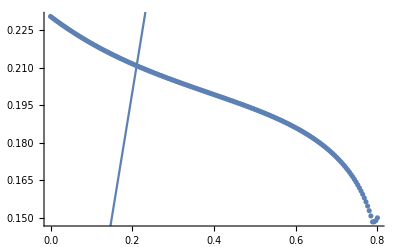

```mathematica
ListPlot[tmp,DataRange->{0,.8},Epilog->{First@ Plot[x,{x,0,1}]}]
```

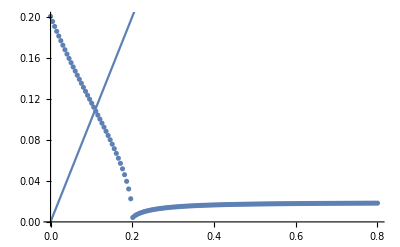

```mathematica
ListPlot[tmp,DataRange->{0,.8},Epilog->{First@ Plot[x,{x,0,1}]},PlotRange->Full]
```

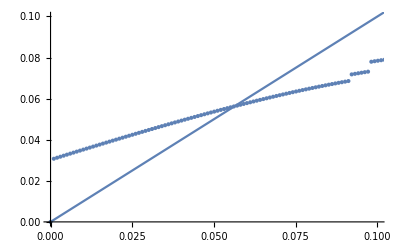

```mathematica
ListPlot[tmp,DataRange->{0,.8},Epilog->{First@ Plot[x,{x,0,1}]},PlotRange->{{0,0.1},{0,0.1}}]
```

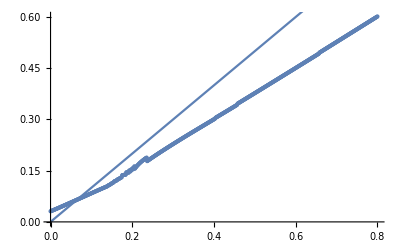

```mathematica
ListPlot[tmp,DataRange->{0,.8},Epilog->{First@ Plot[x,{x,0,1}]},PlotRange->Full]
```

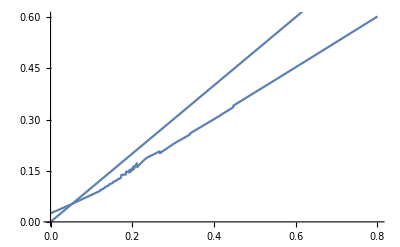

```mathematica
ListLinePlot[tmp,DataRange->{0,.8},Epilog->{First@ Plot[x,{x,0,1}]},PlotRange->Full]
```

```mathematica
f=Interpolation[Transpose@{DeleteCases[Range[0,0.8,0.005],.2],tmp}]
```

InterpolatingFunction[…]

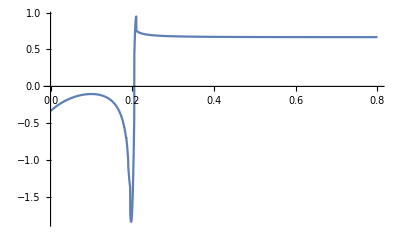

```mathematica
Plot[f'[x],{x,0,0.8}]
```

#### Iteration all

```mathematica
Hcon[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,γ0_?NumberQ,ω0_?NumberQ,dim_?IntegerQ]:=Block[{t=25/a^2,μ=μ0,α=α0/(2a),Vz=V0,Δ=Δ0,γ=γ0,ω=ω0(*,h*)},h=KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]-γ(ω/(√Abs[Δ^2-ω^2])IdentityMatrix[4dim,SparseArray]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ/(√Abs[Δ^2-ω^2])IdentityMatrix[dim,SparseArray]]])]
```

```mathematica
Hiter2[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,γ0_?NumberQ,ω0_?NumberQ,dim_?IntegerQ,n_?NumberQ]:=Block[{t=25/a^2,μ=μ0,α=α0/(2a),Vz=V0,Δ=Δ0,γ=γ0,ω=ω0(*,h*)},h=KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]-γ(ω/(√Abs[Δ^2-ω^2])IdentityMatrix[4dim,SparseArray]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ/(√Abs[Δ^2-ω^2])IdentityMatrix[dim,SparseArray]]]);(Transpose@SortBy[Transpose@Eigensystem[h],First])[[All,n]]]
```

```mathematica
iter2[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,γ0_?NumberQ,dim_?IntegerQ,n_?IntegerQ]:=Block[{half},half=FixedPoint[Hiter2[a,μ0,Δ0,V0,α0,γ0,#,dim,n]&,0,300,SameTest->(Abs[#1-#2]<1*^-6&)];half]
```

```mathematica
ll2=Hiter2[1,0.2,0.2,0,5,0.2,sl[[#]],2,#]&/@Range[8]
```

{{-74.7247,{-2.51556×10^-6,2.52587×10^-6,2.29025×10^-7,2.2419×10^-8,-0.704194,0.707079,0.0641123,0.00627586}},{-74.7247,{-2.46279×10^-7,-5.08922×10^-9,-2.51393×10^-6,2.52596×10^-6,-0.068942,-0.00142465,-0.703738,0.707105}},{-24.4753,{-2.50895×10^-6,-1.79797×10^-7,-0.0000232826,-0.0000234167,-0.0757598,-0.0054291,-0.703037,-0.707086}},{-24.4753,{0.0000232435,0.0000234116,-2.84878×10^-6,-5.21825×10^-7,0.701855,0.706931,-0.086021,-0.0157569}},{24.4753,{0.703722,0.707106,-0.0691086,0.00125724,-0.0000233053,-0.0000234174,2.28869×10^-6,-4.16362×10^-8}},{24.4753,{-0.0532637,0.0171605,-0.705098,-0.706899,1.76394×10^-6,-5.68309×10^-7,0.0000233509,0.0000234105}},{74.7247,{-0.07347,0.00312645,-0.70328,0.7071,2.62454×10^-7,-1.11685×10^-8,2.51229×10^-6,-2.52594×10^-6}},{74.7247,{0.661062,-0.632806,0.250993,-0.315525,-2.36148×10^-6,2.26055×10^-6,-8.9661×10^-7,1.12714×10^-6}}}

```mathematica
vv=Transpose@ll2[[All,2]]
```

{{-2.51556×10^-6,-2.46279×10^-7,-2.50895×10^-6,0.0000232435,0.703722,-0.0532637,-0.07347,0.661062},{2.52587×10^-6,-5.08922×10^-9,-1.79797×10^-7,0.0000234116,0.707106,0.0171605,0.00312645,-0.632806},{2.29025×10^-7,-2.51393×10^-6,-0.0000232826,-2.84878×10^-6,-0.0691086,-0.705098,-0.70328,0.250993},{2.2419×10^-8,2.52596×10^-6,-0.0000234167,-5.21825×10^-7,0.00125724,-0.706899,0.7071,-0.315525},{-0.704194,-0.068942,-0.0757598,0.701855,-0.0000233053,1.76394×10^-6,2.62454×10^-7,-2.36148×10^-6},{0.707079,-0.00142465,-0.0054291,0.706931,-0.0000234174,-5.68309×10^-7,-1.11685×10^-8,2.26055×10^-6},{0.0641123,-0.703738,-0.703037,-0.086021,2.28869×10^-6,0.0000233509,2.51229×10^-6,-8.9661×10^-7},{0.00627586,0.707105,-0.707086,-0.0157569,-4.16362×10^-8,0.0000234105,-2.52594×10^-6,1.12714×10^-6}}

```mathematica
sl=iter2[1,0.2,0.2,0,5,0.2,2,#]&/@Range[8]
```

{-74.7247,-74.7247,-24.4753,-24.4753,24.4753,24.4753,74.7247,74.7247}

```mathematica
Hcon[1,0.2,0.2,0,5,0.2,sl[[#]],2]&[1]
```

SparseArray[…]

```mathematica
Inverse[Transpose@vv].Hcon[1,0.2,0.2,0,5,0.2,sl[[#]],2]&[1].Transpose@vv
```

{{-45.9806,-5.03966,-23.7162,-0.695517,0.00194631,0.000924966,0.000890096,0.00108915},{-5.57609,-46.2495,-0.800778,-24.8938,0.0021978,0.00184449,0.000498609,0.000701338},{-24.8573,-0.784508,-53.2053,5.28243,0.000773496,0.000735769,0.00122878,0.0013483},{-0.761623,-23.7527,5.3205,-52.9646,0.000980459,0.000817938,0.00136012,0.00228896},{0.00198641,0.00214169,0.000620053,0.00111478,52.9992,2.72619,-0.105881,24.7684},{0.000980053,0.00177761,0.000594505,0.000967492,2.73225,48.011,24.9234,-0.00487291},{0.000771788,0.000629677,0.00125678,0.00134578,-0.105886,24.87,52.0001,-2.71624},{0.000965028,0.000815756,0.00136162,0.00228775,24.8218,-0.00486867,-2.72188,46.9898}}

```mathematica
DiagonalMatrix[{a,b}].DiagonalMatrix[{c,D}]
```

{{a c,0},{0,b D}}

```mathematica
Inverse@{{0,a},{b,0}}.DiagonalMatrix[{a,b}]
```

{{0,1},{1,0}}

```mathematica
DiagonalMatrix[{a,b,c}]*
```

{{a,0,0},{0,b,0},{0,0,c}}

```mathematica
SparseArray[Band[{1,5},Automatic,{1,-1}]->x,{5,5}]
```

SparseArray[…]

#### Im

```mathematica
HIm[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,γ0_?NumberQ,ω0_?NumberQ,dim_?IntegerQ,η_?NumberQ]:=Block[{t=25/a^2,μ=μ0,α=α0/(2a),Vz=V0,Δ=Δ0,γ=γ0,ω=ω0},KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]-γ(ω/(√(Δ^2-ω^2))IdentityMatrix[4dim,SparseArray]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ/(√(Δ^2-ω^2))IdentityMatrix[dim,SparseArray]]])-(ω-I η) IdentityMatrix[4*dim,SparseArray]]
```

```mathematica
lt=ParallelTable[Im[Tr[Inverse@HIm[1,.2,.2,0.,2.5,.2,ii,300,0.0001]]],{ii,0,.19,0.001}];//AbsoluteTiming
```

{50.582,Null}

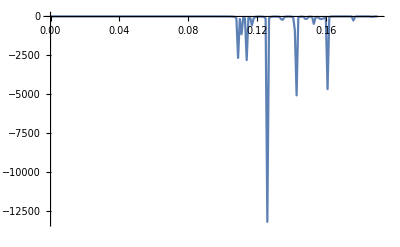

```mathematica
ListLinePlot[lt,PlotRange->Full,DataRange->{0,0.19}]
```

```mathematica
FindPeaks[-lt]
```

{{110,2665.11},{115,2803.6},{127,13198.6},{136,209.215},{144,5069.94},{149,153.342},{154,479.349},{162,4670.},{177,257.45},{188,27.8965}}

```mathematica
Tr@Inverse@Partition[Range[4],2]
```

-5/2

### Run

```mathematica
singm[1,.2,.2,0,2,.2,.2,100]//AbsoluteTiming
```

{0.218971,0.141421}

```mathematica
listt=ParallelTable[SingularValueDecomposition[Hse[1,.2,.2,0.,2.5,.25,i,300],-1,Method->{"Arnoldi",MaxIterations->∞}][[2,1,1]],{i,0,0.2,0.001}];
```

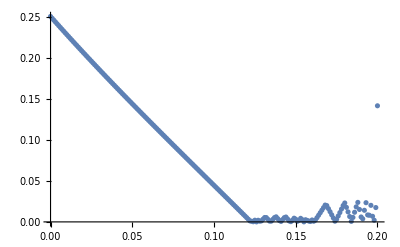

```mathematica
ListPlot[listt,DataRange->{0,0.2}]
```

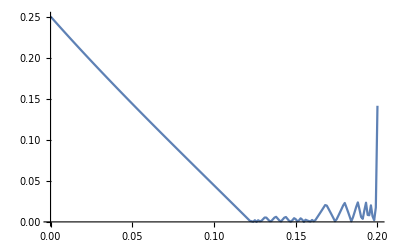

```mathematica
ListLinePlot[listt,DataRange->{0,0.2}]
```

```mathematica
frootz[1,.2,.2,0.1,5,.25,300]
```

0.100469

#### γ=.2

```mathematica
enlist
```

{0.108855,0.108228,0.106998,0.105174,0.102563,0.0994846,0.0961297,0.0925791,0.0888955,0.0851276,0.081313,0.0774793,0.0736431,0.0696077,0.0654597,0.0613563,0.0573165,0.0533415,0.0491383,0.044885,0.0407102,0.0362829,0.031793,0.0268889,0.0220164,0.0172557,0.0126904,0.0084662,0.00485864,0.00227239,0.000883067,0.000321936,0.000131555,0.0000757487,0.0000655661,0.0000696429,0.0000759991,0.0000789107,0.0000747456,0.0000608268,0.000035332,2.45109×10^-6,0.0000517867,0.000110209,0.000173396,0.00023526,0.000288315,0.000324312,0.000335119,0.00031377,0.000255577}

```mathematica
frootz[1,.2,.2,0,2.5,.2,300]//AbsoluteTiming
```

{0.00045197,0.108855}

```mathematica
frootz[1,.2,.2,0.36,5,.2,300]//AbsoluteTiming
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{15.0414,0.00015646}

```mathematica
Monitor[enlist=Table[frootz[1,.2,.2,ii,2.5,.2,300],{ii,0,0.5,0.01}];,ii]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

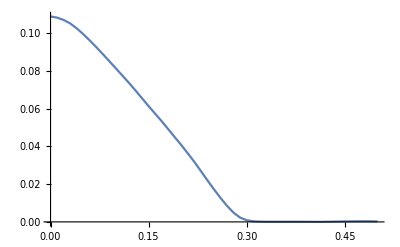

```mathematica
ListLinePlot[enlist,DataRange->{0,0.5}]
```

```mathematica
Monitor[eniter2=Table[iter[.25,.2,.2,ii,2.5,.2,300,1],{ii,0,0.5,0.01}],ii]//AbsoluteTiming
```

{94.6572,{0.117344,0.115521,0.112988,0.109985,0.10662,0.102961,0.0990642,0.0949772,0.0907422,0.0863944,0.081965,0.077479,0.0729586,0.0684233,0.063891,0.0593784,0.0549015,0.0504779,0.0461241,0.0418585,0.037701,0.0336732,0.0298008,0.0261107,0.0226329,0.0194019,0.0164521,0.0138187,0.0115359,0.00963125,0.00812391,0.00702156,0.00632091,0.00600571,0.00605099,0.00642568,0.00709565,0.00802605,0.0091835,0.0105348,0.0120505,0.0137023,0.015464,0.0173107,0.0192187,0.0211647,0.0231264,0.0250802,0.0270033,0.0288722,0.0306625}}

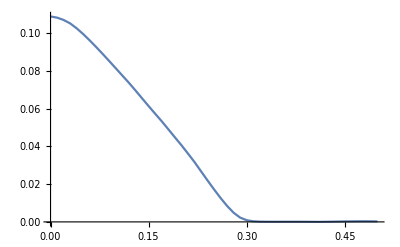

```mathematica
ListLinePlot[eniter,DataRange->{0,0.5}]
```

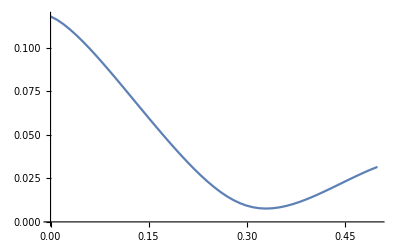

```mathematica
ListLinePlot[eniter,DataRange->{0,0.5}]
```

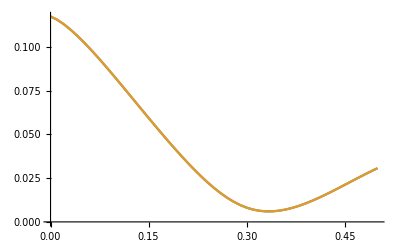

```mathematica
ListLinePlot[{eniter2,eniter2},DataRange->{0,0.5}]
```

```mathematica
ttt=ParallelTable[iter[1,.2,.2,ii,2.5,.7,300,1],{ii,Range[0,1,0.005]}]
```

{0.17618,0.175942,0.175366,0.1746,0.173742,0.172829,0.17188,0.170903,0.169906,0.16889,0.167859,0.166813,0.165754,0.164684,0.163602,0.16251,0.161408,0.160296,0.159175,0.158045,0.156907,0.15576,0.154606,0.153445,0.152276,0.151101,0.149918,0.14873,0.147535,0.146335,0.145129,0.143917,0.1427,0.141478,0.140252,0.13902,0.137785,0.136545,0.135301,0.134053,0.132802,0.131547,0.130288,0.129027,0.127762,0.126491,0.125219,0.123943,0.122665,0.121384,0.120102,0.118817,0.11753,0.116242,0.114952,0.113661,0.112368,0.111074,0.109778,0.108482,0.107184,0.105885,0.104584,0.10328,0.101976,0.100672,0.0993667,0.0980611,0.0967552,0.0954491,0.0941427,0.0928358,0.0915272,0.090217,0.0889068,0.0875966,0.0862867,0.0849773,0.0836638,0.0823495,0.0810351,0.0797209,0.0784072,0.0770944,0.0757826,0.0744719,0.0731627,0.0718549,0.0705487,0.0692443,0.0679417,0.0666411,0.0653425,0.064046,0.0627518,0.06146,0.0601705,0.0588835,0.0575992,0.0563175,0.0550385,0.0537624,0.0524893,0.0512192,0.0499521,0.0486882,0.0474276,0.0461704,0.0449165,0.0436662,0.0424195,0.0411765,0.0399373,0.038702,0.0374706,0.0362434,0.0350203,0.0338015,0.0325872,0.0313774,0.0301724,0.0289721,0.0277769,0.0265868,0.0254021,0.024223,0.0230498,0.0218827,0.020722,0.0195682,0.0184217,0.017283,0.0161527,0.0150317,0.0139207,0.012821,0.0117339,0.0106613,0.0096054,0.00856913,0.00755629,0.0065718,0.00562213,0.00471568,0.00386316,0.00307766,0.002374,0.00176664,0.00126605,0.000874603,0.000584628,0.000380181,0.000242114,0.000151783,0.0000940825,0.0000578544,0.0000354605,0.0000216089,0.0000131389,7.97969×10^-6,4.75963×10^-6,2.89041×10^-6,1.75646×10^-6,1.06834×10^-6,7.43233×10^-7,4.5255×10^-7,2.75241×10^-7,1.66711×10^-7,9.99498×10^-8,5.85895×10^-8,3.27032×10^-8,1.62692×10^-8,5.63876×10^-9,1.39032×10^-9,6.13404×10^-9,9.36161×10^-9,1.15016×10^-8,1.27675×10^-8,1.32354×10^-8,1.28915×10^-8,1.16642×10^-8,9.44464×10^-9,6.10298×10^-9,1.50119×10^-9,4.4949×10^-9,1.20039×10^-8,2.11167×10^-8,3.18842×10^-8,4.4304×10^-8,5.83077×10^-8,7.37478×10^-8,9.03859×10^-8,1.07882×10^-7,1.25787×10^-7,1.43536×10^-7,1.60446×10^-7,1.75722×10^-7,1.88462×10^-7,1.97671×10^-7,2.02283×10^-7,2.01184×10^-7}

```mathematica
ttt[[11;;20]]
```

{0.167859,0.166813,0.165754,0.164684,0.163602,0.16251,0.161408,0.160296,0.159175,0.158045}

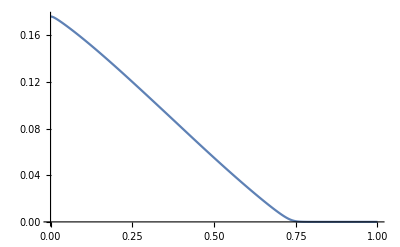

```mathematica
ListLinePlot[ttt,DataRange->{0,1}]
```

```mathematica
Monitor[eniter2=Table[iter[1,.2,.2,ii,2.5,.2,300,1],{ii,0,0.5,0.01}],ii]//AbsoluteTiming
```

{19.4391,{0.118185,0.117554,0.11636,0.114606,0.112095,0.108961,0.105508,0.101822,0.0979668,0.0939997,0.0899616,0.0858869,0.081792,0.0774042,0.0729069,0.0684492,0.0640522,0.0597139,0.0550616,0.0503749,0.0457657,0.0408309,0.0358206,0.0303465,0.0248981,0.0195569,0.0144158,0.00963812,0.00554334,0.00259481,0.00100988,0.000367274,0.000149501,0.0000872207,0.0000741816,0.0000787942,0.0000875091,0.0000908616,0.0000845674,0.0000688196,0.00003966,3.46599×10^-6,0.0000599758,0.000125244,0.000199005,0.000268016,0.000330288,0.000369983,0.000382311,0.000359449,0.000292784}}

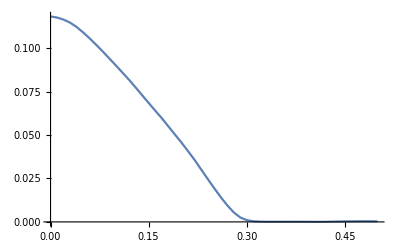

```mathematica
ListLinePlot[eniter2,DataRange->{0,0.5}]
```

#### γ=.4

```mathematica
Monitor[enlist2=Table[frootz[1,.2,.2,ii,2.5,.4,300],{ii,0,0.5,0.01}];,ii]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

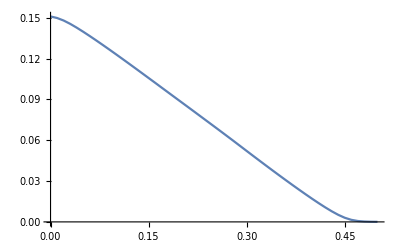

```mathematica
ListLinePlot[enlist2,DataRange->{0,0.5}]
```

#### γ=.6

```mathematica
Monitor[enlist3=Table[frootz[1,.2,.2,ii,2.5,.6,300],{ii,0,1,0.01}];,ii]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

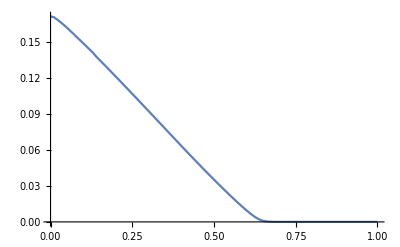

```mathematica
ListLinePlot[enlist3,DataRange->{0,1}]
```

```mathematica
ttt={1,2}
```

{1,2}

```mathematica
ttt.IdentityMatrix[2].ConjugateTranspose[{ttt}]
```

{5}

#### 410

```mathematica
eniter410=ParallelTable[iter[1,.3705,.3,ii,.5818,0.5486,1000,1],{ii,0,√(.3705^2+0.5486^2),0.01}];//AbsoluteTiming
```

{202.103,Null}

```mathematica
int410sc=Interpolation[Transpose@{Range[0,√(.3705^2+0.5486^2),0.01],-eniter410}]
```

InterpolatingFunction[…]

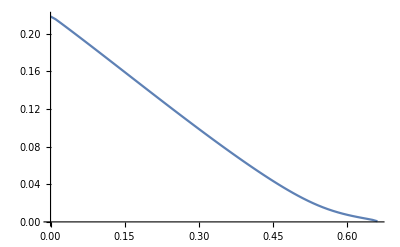

```mathematica
ListLinePlot[eniter410,DataRange->{0,√(.3705^2+0.5486^2)}]
```

```mathematica
dataintse=Interpolation[Transpose@{Range[0,√(.3705^2+0.5486^2),.01],eniter}]
```

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«17»},{-iter[1,0.1484,0.3,0.,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.01,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.02,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.03,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.04,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.05,2.1253,0.8801,1000],«39»,-iter[1,0.1484,0.3,0.45,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.46,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.47,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.48,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.49,2.1253,0.8801,1000],«40»}} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«17»},{-iter[1,0.1484,0.3,0.,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.01,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.02,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.03,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.04,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.05,2.1253,0.8801,1000],«39»,-iter[1,0.1484,0.3,0.45,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.46,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.47,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.48,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.49,2.1253,0.8801,1000],«40»}}] does not contain a list of data and coordinates.

Interpolation[Transpose[{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66},{-iter[1,0.1484,0.3,0.,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.01,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.02,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.03,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.04,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.05,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.06,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.07,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.08,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.09,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.1,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.11,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.12,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.13,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.14,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.15,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.16,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.17,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.18,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.19,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.2,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.21,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.22,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.23,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.24,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.25,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.26,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.27,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.28,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.29,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.3,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.31,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.32,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.33,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.34,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.35,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.36,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.37,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.38,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.39,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.4,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.41,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.42,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.43,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.44,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.45,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.46,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.47,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.48,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.49,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.5,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.51,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.52,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.53,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.54,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.55,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.56,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.57,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.58,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.59,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.6,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.61,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.62,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.63,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.64,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.65,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.66,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.67,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.68,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.69,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.7,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.71,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.72,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.73,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.74,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.75,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.76,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.77,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.78,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.79,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.8,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.81,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.82,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.83,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.84,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.85,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.86,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.87,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.88,2.1253,0.8801,1000],-iter[1,0.1484,0.3,0.89,2.1253,0.8801,1000]}}]]

#### 590

```mathematica
eniter590=ParallelTable[iter[1,0.1484,.3,ii,2.1253,0.8801,1000,1],{ii,0,√(0.1484^2+0.8801^2),0.01}];//AbsoluteTiming
```

{34.1063,Null}

```mathematica
int590sc=Interpolation[Transpose@{Range[0,√(0.1484^2+0.8801^2),0.01],-eniter590}]
```

InterpolatingFunction[…]

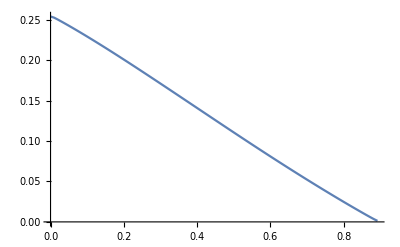

```mathematica
ListLinePlot[eniter590,DataRange->{0,√(0.1484^2+0.8801^2)}]
```

#### 410Best fit

```mathematica
0.8747 0.5557 1.0140
```

```mathematica
bestfit410=ParallelTable[iter[1,0.8747,.3,ii,1.0140,0.5557,300,1],{ii,0,√(0.8747^2+0.5557^2),0.01}];//AbsoluteTiming
```

{75.4756,Null}

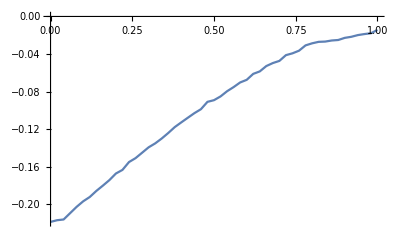

```mathematica
ListLinePlot[line2]
```

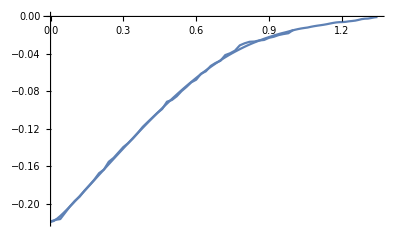

```mathematica
ListLinePlot[-bestfit410,DataRange->{0,√(0.8747^2+0.5557^2)*1.3},Epilog->{ First@ListLinePlot[line2]}]
```

```mathematica
int410=Interpolation[Transpose@{Range[0,√(0.8747^2+0.5557^2),.01],-bestfit410}]
```

InterpolatingFunction[…]

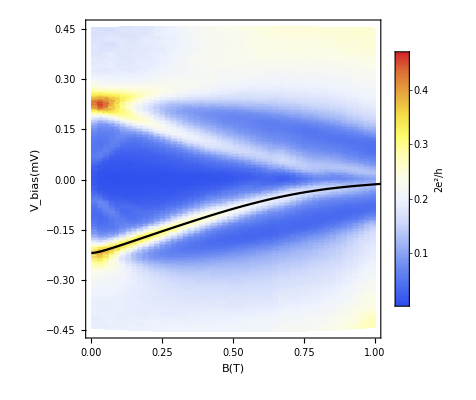

```mathematica
ListDensityPlot[ndata[[3]],ColorFunction->"TemperatureMap",PlotLegends->BarLegend[Automatic,LegendLabel->"2e^2/h"],FrameLabel->{"B(T)","V_bias(mV)"},Epilog->{ First@Plot[int410[x/1.3],{x,0,1.2},PlotStyle->Black](*,First@ListLinePlot[line2,PlotStyle->Black]*)(*,Line[{{0,-.25},{1,-.5*^-1}}],Line[{{0,0},{1,0}}]*)} ]
```

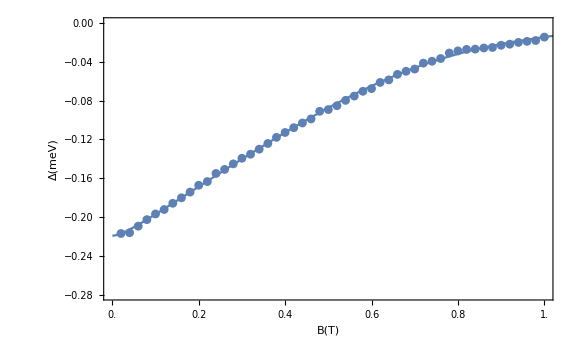

```mathematica
ListPlot[Most@line2,PlotRange->{{0,1},{-0.28,0}},Epilog->{First@Plot[int410[x/1.3],{x,0,1.2}]},FrameLabel->{{Rotate["Δ(meV)",-90Degree],None},{"B(T)","V(meV)"}},Frame->True,FrameTicks->{Automatic,{Range[0,1.2,.2],Transpose@{Range[0,.4,.1]*4.3,Range[0,.4,.1]}}},FrameTicksStyle->20,ImageSize->Large]
```

```mathematica
Plot[{-dataint'[x0/3.25]/3.25,Abs@D[ss,x]/.x->x0},{x0,0,1},PlotRange->{0,0.4},FrameLabel->{{Rotate["(∂ Δ)/(∂ B)",-90Degree],Rotate["g",-90Degree]},{"B(T)","V(meV)"}},Frame->True,FrameTicks->{{Range[0,.4,0.1],Transpose@{Range[0,20,4]/(2/(5.788381*^-2)),Range[0,20,4]}},{Range[0,1,.2],Transpose@{Range[0,.3,.1]*3.25,Range[0,.3,.1]}}},FrameTicksStyle->20,ImageSize->Large]
```

#### 590Bestfit

```mathematica
0.7064 0.7994 4.9926
```

```mathematica
bestfit590=ParallelTable[iter[1,0.7064,.3,ii,4.9926,0.7994,1000,1],{ii,0,√(0.7064^2+0.7994^2),0.01}];//AbsoluteTiming
```

{314.852,Null}

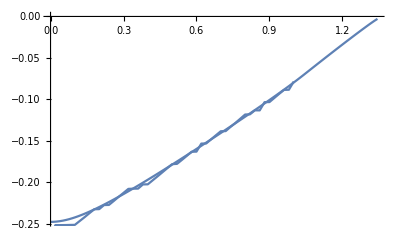

```mathematica
ListLinePlot[-bestfit590,DataRange->{0,√(0.7064^2+0.7994^2)*1.26},Epilog->{ First@ListLinePlot[line]}]
```

```mathematica
bestfit5902=ParallelTable[iter[1,0.6535,.3,ii,4.9982,0.7998,1000,1],{ii,0,√(0.7064^2+0.7994^2),0.01}];//AbsoluteTiming
```

{196.32,Null}

```mathematica
ListLinePlot[-bestfit5902,DataRange->{0,√(0.7064^2+0.7994^2)*1.26},Epilog->{ First@ListLinePlot[line]}]
```

-Graphics-

```mathematica
int590=Interpolation[Transpose@{Range[0,√(0.7064^2+0.7994^2),.01],-bestfit590}]
```

InterpolatingFunction[…]

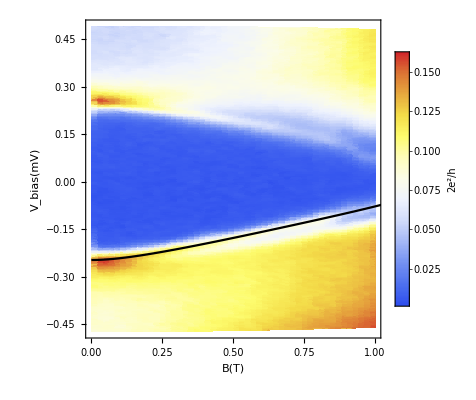

```mathematica
ListDensityPlot[ndata[[22]],ColorFunction->"TemperatureMap",PlotLegends->BarLegend[Automatic,LegendLabel->"2e^2/h"],FrameLabel->{"B(T)","V_bias(mV)"},Epilog->{ First@Plot[int590[x/1.26],{x,0,1.2},PlotStyle->Black](*,Line[{{0,-.35},{1,-1*^-1}}],Line[{{0,-2*^-1},{1,-.5*^-1}}]*)} ]
```

### Legacy

```mathematica
FindPeaks[-list]
```

{{110,-0.000344278},{123,-0.000682039},{139,-0.000736305},{141,-0.0000501941},{183,-0.00161806},{198,-0.00565939}}

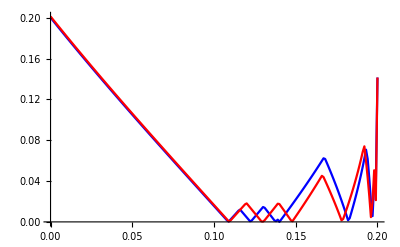

```mathematica
ListLinePlot[{list,listt},DataRange->{0,0.2},PlotStyle->{Blue,Red}]
```

```mathematica
Interpolation[Transpose@{Range[0,0.2,0.001],list}]
```

InterpolatingFunction[…]

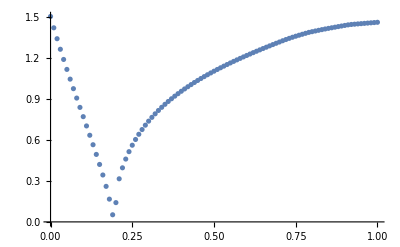

```mathematica
ListPlot[list,DataRange->{0,1},PlotRange->{0,Automatic}]
```

```mathematica
ls=Solve[x*√(1+x)==γ √(1-x),{x}][[1,1,2]]
```

-1/3-(-1+3 γ^2)/(3 (-1+18 γ^2+3 √3 √(-γ^2+11 γ^4+γ^6))^(1/3))+1/3 (-1+18 γ^2+3 √3 √(-γ^2+11 γ^4+γ^6))^(1/3)

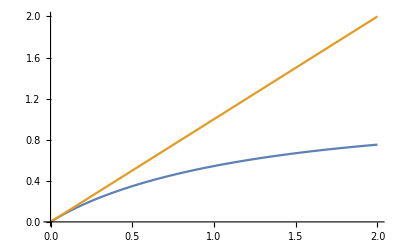

```mathematica
Plot[{ls/.γ->γ0,γ0},{γ0,0,2}]
```

```mathematica
(ls/.γ->1.)*.2
```

0.108738

```mathematica
√(.2^2+0.10873780253841524^2)
```

0.227649

```mathematica
(ls/.γ->1/.2)*.2
```

0.186548

```mathematica
√(1^2+.2^2)
```

1.0198

```mathematica
ls=Table[Solve[x*√(1+x)==γ √(1-x),{x}]/.γ->γ0,{γ0,0,2.5,.1}]
```

{{{x→5.55112×10^-17+0. ⅈ},{x→-1.+0. ⅈ},{x→-5.55112×10^-17+0. ⅈ}},{{x→0.0912552+0. ⅈ},{x→-0.979363-2.77556×10^-17 ⅈ},{x→-0.111892+0. ⅈ}},{{x→0.168681+0. ⅈ},{x→-0.907326-2.77556×10^-17 ⅈ},{x→-0.261355+5.55112×10^-17 ⅈ}},{{x→0.23589+0. ⅈ},{x→-0.63589+0. ⅈ},{x→-0.6+0. ⅈ}},{{x→0.295101},{x→-0.647551+0.35052 ⅈ},{x→-0.647551-0.35052 ⅈ}},{{x→0.34781},{x→-0.673905+0.514426 ⅈ},{x→-0.673905-0.514426 ⅈ}},{{x→0.39509},{x→-0.697545+0.651626 ⅈ},{x→-0.697545-0.651626 ⅈ}},{{x→0.437747},{x→-0.718873+0.776267 ⅈ},{x→-0.718873-0.776267 ⅈ}},{{x→0.476411},{x→-0.738205+0.89355 ⅈ},{x→-0.738205-0.89355 ⅈ}},{{x→0.511587},{x→-0.755794+1.00602 ⅈ},{x→-0.755794-1.00602 ⅈ}},{{x→0.543689},{x→-0.771845+1.11514 ⅈ},{x→-0.771845-1.11514 ⅈ}},{{x→0.573062},{x→-0.786531+1.22181 ⅈ},{x→-0.786531-1.22181 ⅈ}},{{x→0.6},{x→-0.8+1.32665 ⅈ},{x→-0.8-1.32665 ⅈ}},{{x→0.624753},{x→-0.812376+1.43007 ⅈ},{x→-0.812376-1.43007 ⅈ}},{{x→0.647539},{x→-0.823769+1.5324 ⅈ},{x→-0.823769-1.5324 ⅈ}},{{x→0.668548},{x→-0.834274+1.63386 ⅈ},{x→-0.834274-1.63386 ⅈ}},{{x→0.687947},{x→-0.843973+1.73463 ⅈ},{x→-0.843973-1.73463 ⅈ}},{{x→0.705884},{x→-0.852942+1.83484 ⅈ},{x→-0.852942-1.83484 ⅈ}},{{x→0.722491},{x→-0.861246+1.93462 ⅈ},{x→-0.861246-1.93462 ⅈ}},{{x→0.737885},{x→-0.868943+2.03404 ⅈ},{x→-0.868943-2.03404 ⅈ}},{{x→0.752172},{x→-0.876086+2.13317 ⅈ},{x→-0.876086-2.13317 ⅈ}},{{x→0.765445},{x→-0.882723+2.23207 ⅈ},{x→-0.882723-2.23207 ⅈ}},{{x→0.777791},{x→-0.888896+2.3308 ⅈ},{x→-0.888896-2.3308 ⅈ}},{{x→0.789286},{x→-0.894643+2.42938 ⅈ},{x→-0.894643-2.42938 ⅈ}},{{x→0.8},{x→-0.9+2.52784 ⅈ},{x→-0.9-2.52784 ⅈ}},{{x→0.809996},{x→-0.904998+2.62623 ⅈ},{x→-0.904998-2.62623 ⅈ}}}

```mathematica
Transpose@ls
```

{{{x→5.55112×10^-17+0. ⅈ},{x→0.0912552+0. ⅈ},{x→0.168681+0. ⅈ},{x→0.23589+0. ⅈ},{x→0.295101},{x→0.34781},{x→0.39509},{x→0.437747},{x→0.476411},{x→0.511587},{x→0.543689},{x→0.573062},{x→0.6},{x→0.624753},{x→0.647539},{x→0.668548},{x→0.687947},{x→0.705884},{x→0.722491},{x→0.737885},{x→0.752172},{x→0.765445},{x→0.777791},{x→0.789286},{x→0.8},{x→0.809996}},{{x→-1.+0. ⅈ},{x→-0.979363-2.77556×10^-17 ⅈ},{x→-0.907326-2.77556×10^-17 ⅈ},{x→-0.63589+0. ⅈ},{x→-0.647551+0.35052 ⅈ},{x→-0.673905+0.514426 ⅈ},{x→-0.697545+0.651626 ⅈ},{x→-0.718873+0.776267 ⅈ},{x→-0.738205+0.89355 ⅈ},{x→-0.755794+1.00602 ⅈ},{x→-0.771845+1.11514 ⅈ},{x→-0.786531+1.22181 ⅈ},{x→-0.8+1.32665 ⅈ},{x→-0.812376+1.43007 ⅈ},{x→-0.823769+1.5324 ⅈ},{x→-0.834274+1.63386 ⅈ},{x→-0.843973+1.73463 ⅈ},{x→-0.852942+1.83484 ⅈ},{x→-0.861246+1.93462 ⅈ},{x→-0.868943+2.03404 ⅈ},{x→-0.876086+2.13317 ⅈ},{x→-0.882723+2.23207 ⅈ},{x→-0.888896+2.3308 ⅈ},{x→-0.894643+2.42938 ⅈ},{x→-0.9+2.52784 ⅈ},{x→-0.904998+2.62623 ⅈ}},{{x→-5.55112×10^-17+0. ⅈ},{x→-0.111892+0. ⅈ},{x→-0.261355+5.55112×10^-17 ⅈ},{x→-0.6+0. ⅈ},{x→-0.647551-0.35052 ⅈ},{x→-0.673905-0.514426 ⅈ},{x→-0.697545-0.651626 ⅈ},{x→-0.718873-0.776267 ⅈ},{x→-0.738205-0.89355 ⅈ},{x→-0.755794-1.00602 ⅈ},{x→-0.771845-1.11514 ⅈ},{x→-0.786531-1.22181 ⅈ},{x→-0.8-1.32665 ⅈ},{x→-0.812376-1.43007 ⅈ},{x→-0.823769-1.5324 ⅈ},{x→-0.834274-1.63386 ⅈ},{x→-0.843973-1.73463 ⅈ},{x→-0.852942-1.83484 ⅈ},{x→-0.861246-1.93462 ⅈ},{x→-0.868943-2.03404 ⅈ},{x→-0.876086-2.13317 ⅈ},{x→-0.882723-2.23207 ⅈ},{x→-0.888896-2.3308 ⅈ},{x→-0.894643-2.42938 ⅈ},{x→-0.9-2.52784 ⅈ},{x→-0.904998-2.62623 ⅈ}}}

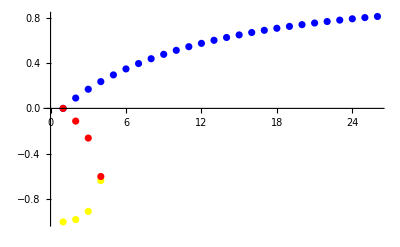

1.024

```mathematica
ListPlot[Transpose@ls[[All,All,1,2]],PlotStyle->{Blue,Yellow,Red}]
```

```mathematica
j
```

```mathematica
Eigenvalues
```

```mathematica
Happrox[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,γ0_?NumberQ,dim_?IntegerQ]:=Block[{t=25/a^2,μ=μ0,α=α0/(2a),Vz=V0,Δ=Δ0,γ=γ0},ei=Eigensystem[Hc[a,μ,γ,Vz,α,dim],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}];psip=SortBy[Select[Transpose@ei,First[#]>0&],Abs@First[#]&][[1,2]];psin=SortBy[Select[Transpose@ei,First[#]<0&],Abs@First[#]&][[1,2]];hse=Hse[a,μ0,Δ0,V0,α0,γ0,ω,dim];hap={{Conjugate[psip].hse.psip,Conjugate[psin].hse.psip},{Conjugate[psip].hse.psin,Conjugate[psin].hse.psin}};NSolve[Chop[Det[hap-ω IdentityMatrix[2]]]==0,ω][[All,1,2]]]
```